# Beugung

```mathematica
Clear["Global`*"];
```

## Messung

```mathematica
y = {{22.1, 22.7},
{23.7, 24.6},
{25.1, 25.7},
{25.8, 26.5},
{30.7, 31.7},
{36.1, 37.4},
{38.7, 40.0}};
```

```mathematica
y = Table[(y[[i]][[1]]+y[[i]][[2]])/2, {i, 1, Length[y]}]
```

{22.4,24.15,25.4,26.15,31.2,36.75,39.35}

```mathematica
d = 80;
```

```mathematica
l = {7065, 6678, 5875, 5015, 4921, 4713, 4471};
```

```mathematica
Mean[l]
```

5534

```mathematica
g[x_, ll_] = ll/Sin[ArcTan[x/d]];
```

```mathematica
Table[g[y[[i]], l[[Length[l]-i+1]]]*10^-10, {i, 1, Length[l]}]
```

{1.6582×10^-6,1.63083×10^-6,1.62617×10^-6,1.61411×10^-6,1.61692×10^-6,1.59976×10^-6,1.60069×10^-6}

```mathematica
g1 = Mean[%]
```

1.62095×10^-6

## Mikroskop

```mathematica
n = 12;
```

```mathematica
d2 = 0.0208;
```

```mathematica
g2 = d2/n/1000
```

1.73333×10^-6

```mathematica
g=(g2+g1)/2
```

1.67714×10^-6

```mathematica
Abs[(g1-g2)/g]
```

0.0670063

## H

```mathematica
rot= {34.6,35.4}
```

{34.6,35.4}

```mathematica
blau = {24.5 , 25.4}
```

{24.5,25.4}

```mathematica
lambdarot = g*Sin[ArcTan[Mean[rot]/d]]
```

6.72231×10^-7

```mathematica
lambdablau = g*Sin[ArcTan[Mean[blau]/d]]
```

4.99338×10^-7

```mathematica
c=2.99*10^8;
```

```mathematica
frot = c/lambdarot
```

4.44788×10^14

```mathematica
fblau = c/lambdablau
```

5.98792×10^14

```mathematica
R  = 3.288*10^15
```

3.288×10^15

```mathematica
fff[m_, nn_] = R*(1/m^2-1/nn^2)
```

3.288×10^15 (1/m^2-1/nn^2)

```mathematica
fff[2,3]
```

4.56667×10^14

```mathematica
fff[2,4]
```

6.165×10^14

```mathematica
h = 6.63*10^-34;
```

```mathematica
e = 1.602*10^-19;
```

```mathematica
EE[v_] = h*c/v;
```

```mathematica
EE[lambdarot]/e
```

1.84079

3>2

```mathematica
EE[lambdablau]/e
```

2.47815

4 > 2

```mathematica
En[nn_] = -12.6/nn^2;
```

```mathematica
En[3] - En[2]
```

1.75

```mathematica
En[4] - En[2]
```

2.3625

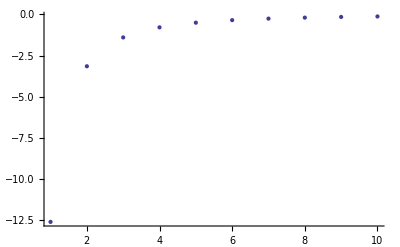

```mathematica
ListPlot[Table[En[n], {n, 1, 10}]]
```

## Fehler

```mathematica
y = Mean[y]/100
```

0.293429

```mathematica
d = d/100
```

4/5

```mathematica
s = Sqrt[(Mean[l]/10^10*(y^2+d^2)^(3/2)/d^2)^2*0.001^2 + 
(Mean[l]/10^10*(y^2+d^2)^(3/2)/d/y)^2*0.0005^2 ]
```

9.04498×10^-10

```mathematica
y = Mean[{Mean[rot], Mean[blau]}]/100
```

0.29975

```mathematica
s=Sqrt[(g*d^2/(d^2+y^2)^(3^2))^2*0.001^2+(g*d*y/(d^2+y^2)^(3^2))^2*0.0005^2]
```

1.8584×10^-8

```mathematica
1/(4994/158)//N
```

0.031638

```mathematica
c/Mean[{lambdarot, lambdablau}]*s
```

9.48574×10^6